# Deutsch-Jozsa Algorithm

We will discuss the Deutsch-Jozsa algorithm. It decides whether a promised function on n-bit inputs is constant or balanced using a single oracle call. The Deutsch-Jozsa circuit is designed in a way that if the function is constant, all amplitude concentrates on the all-zeros output; if balanced, that outcome vanishes and some nonzero string appears. A bit-flip oracle and a phase oracle are equivalent here because initializing the target in the minus state turns the bit flip into an input-dependent phase.

## Key Concepts

Boolean function

Constant Boolean function

Balanced Boolean function

Deutsch-Jozsa

## Statement of the Deutsch-Jozsa Problem

You’re given black-box access to a Boolean function, f, with the promise that f is either constant, i.e. f(x) is the same for every x (either all 0s or all 1s), or balanced, i.e, f(x)=0 for exactly half of all inputs and f(x)=1 for the other half.

Let’s consider Xor in 2 variables, as a specific case, which is a balanced function. Keep in mind that you have a black=box access to it, and being told that it is either constant or balanced.

```mathematica
Counts@BooleanTable[Xor[x,y,z],{x,y,z}]
```

<|True→4,False→4|>

Let’s adopt a deterministic (always correct) classical algorithm. You query inputs one by one, observing f(x). If you ever see both outputs 0 and 1, you can confidently say “balanced.” If all outputs seen so far are identical, you still don’t know: the function might be truly constant, or it might be balanced but you’ve only hit inputs from the “same half” so far. Therefore, any deterministic classical algorithm that is always correct needs, in the worst case, 2^(n-1)+1 queries (that’s exponential in n.)

Consider Xor in 3 variables as a specific example (n=3). An adversary can keep you uncertain for a long time. For example, the inputs order can be like this:

```mathematica
allInputs=SortBy[Tuples[{True,False},3],Apply[Xor]]
```

{{False,False,False},{False,True,True},{True,False,True},{True,True,False},{False,False,True},{False,True,False},{True,False,False},{True,True,True}}

The outcome of f queries on the list of inputs:

```mathematica
Xor@@@allInputs
```

{False,False,False,False,True,True,True,True}

Up to the fourth query, all outcomes are identical, so you cannot decide yet. The fifth query produces a different outcome, confirming the function is balanced. Let’s walk through the procedure step by step.

```mathematica
classicalDJ[Xor,allInputs]
```

The result of query-2 is the same as previous one, so still cannot determined if the function is balanced or constant.

The result of query-3 is the same as previous one, so still cannot determined if the function is balanced or constant.

The result of query-4 is the same as previous one, so still cannot determined if the function is balanced or constant.

After 5 queries, it is determined that the function is balanced

Now let’s consider a different order of inputs, for example, by swtiching 3rd and 5th elements in the previous list:

```mathematica
{allInputs[[3]],allInputs[[5]]}={allInputs[[5]],allInputs[[3]]};
Xor@@@allInputs
```

{False,False,True,False,False,True,True,True}

This time, after the third query, you can conclude the function is balanced. Let’s walk through the steps.

```mathematica
classicalDJ[Xor,allInputs]
```

The result of query-2 is the same as previous one, so still cannot determined if the function is balanced or constant.

After 3 queries, it is determined that the function is balanced

## Deutsch-Jozsa oracles

Consider the following balanced Boolean function on three input bits:

```mathematica
boo=(x&&!y)||(x&&!z)||(!y&&!z);
```

Show its truth table:

```mathematica
ResourceFunction["TruthTable"][boo,{x,y,z}]
```

x | y | z | (x&&!y)||(x&&!z)||(!y&&!z)
True | True | True | False
True | True | False | True
True | False | True | True
True | False | False | True
False | True | True | False
False | True | False | False
False | False | True | False
False | False | False | True

Show explicitly that this function is balanced by listing all eight inputs and verifying that four outputs are 1 and four are 0.

```mathematica
Counts@BooleanTable[boo]
```

<|False→4,True→4|>

The quantum Deutsch–Jozsa algorithm can use two oracle types. The Boolean oracle acts on an n-qubit input register plus one ancilla qubit: it leaves the input unchanged and flips the ancilla exactly when the function evaluates to 1.

The above bit oracle acts as U_f xy=xy⊕f(x) where x represents n-qubit case and y the ancillary one (the last qubit)

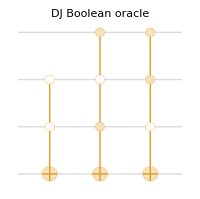
-Graphics-  xy | DJxy | xy⊕f(x)
1111 | 1111 | {1,1,1,1}
1110 | 1110 | {1,1,1,0}
1101 | 1100 | {1,1,0,0}
1100 | 1101 | {1,1,0,1}
1011 | 1010 | {1,0,1,0}
1010 | 1011 | {1,0,1,1}
1001 | 1000 | {1,0,0,0}
1000 | 1001 | {1,0,0,1}  xy | DJxy | xy⊕f(x)
0111 | 0111 | {0,1,1,1}
0110 | 0110 | {0,1,1,0}
0101 | 0101 | {0,1,0,1}
0100 | 0100 | {0,1,0,0}
0011 | 0011 | {0,0,1,1}
0010 | 0010 | {0,0,1,0}
0001 | 0000 | {0,0,0,0}
0000 | 0001 | {0,0,0,1}

```mathematica
With[{op=QuantumCircuitOperator["DeutschJozsaBooleanOracle"[boo]]},Row[Riffle[{op["Diagram","WireLabels"->None,ImageSize->200,PlotLabel->"DJ Boolean oracle"],Sequence@@(TableForm[#,TableHeadings->{None, {"xy","DJxy","xy⊕f(x)"}},TableDepth->2]&/@Partition[Transpose[Append[Transpose[{TraditionalForm[#],TraditionalForm[op[#]]}&/@Table[QuantumState["Register"[4,i]],{i,2^4-1,0,-1}]],Riffle[Boole@Append[#,Xor[boo/.Thread[{x,y,z}->#],True]]&/@Tuples[{True,False},3],Boole@Append[#,Xor[boo/.Thread[{x,y,z}->#],False]]&/@Tuples[{True,False},3]]]],UpTo@8])},"  "]]]
```

An important feature: if the ancilla is initialized in the minus state, the Boolean oracle leaves it unchanged and instead tags solutions by a negative phase on the corresponding n-qubit terms.

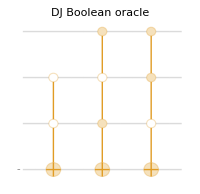
-Graphics-  xy | DJxy
111 𝓍_− | 111 𝓍_−
110 𝓍_− | -110 𝓍_−
101 𝓍_− | -101 𝓍_−
100 𝓍_− | -100 𝓍_−
011 𝓍_− | 011 𝓍_−
010 𝓍_− | 010 𝓍_−
001 𝓍_− | 001 𝓍_−
000 𝓍_− | -000 𝓍_−

```mathematica
op=QuantumCircuitOperator["DeutschJozsaBooleanOracle"[boo]];
Row[{op["Diagram","WireLabels"->{"","","","-"},ImageSize->200,PlotLabel->"DJ Boolean oracle"],,"  ",TableForm[{TraditionalForm[QuantumState[#,{2,2,2,"X"}]],TraditionalForm[QuantumState[op[#],{2,2,2,"X"}]]}&/@Table[QuantumTensorProduct[QuantumState["Register"[3,i]],QuantumState["-"]],{i,2^3-1,0,-1}],TableHeadings->{None, {"xy","DJxy"}},TableDepth->2]}]
```

The Deutsch–Jozsa phase oracle uses no ancilla and applies a negative phase to input states that satisfy the function.

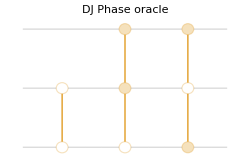
-Graphics-  xy | DJxy
111 | 111
110 | -110
101 | -101
100 | -100
011 | 011
010 | 010
001 | 001
000 | -000

```mathematica
op=QuantumCircuitOperator["DeutschJozsaPhaseOracle"[boo]];
Row[{op["Diagram","WireLabels"->None,ImageSize->250,PlotLabel->"DJ Phase oracle"],,"  ",TableForm[{TraditionalForm[#],TraditionalForm[op[#]]}&/@Table[QuantumState["Register"[3,i]],{i,2^3-1,0,-1}],TableHeadings->{None, {"xy","DJxy"}},TableDepth->2]}]
```

Find all constant and balanced Boolean functions on three input bits. (Constant: all 0s or all 1s; Balanced: four 1s and four 0s across the eight inputs.)

```mathematica
threeVariableBooleans=With[{allBoo=BooleanFunction[#,3] & /@ Range[0,2^(2^3)-1]},
<|"Balanced"->Select[allBoo,
  Count[True][BooleanTable[#]]==Count[False][BooleanTable[#]] &],"Constant"->Select[allBoo,
  Count[True][BooleanTable[#]]==0||Count[False][BooleanTable[#]]==0 &]|>];
```

For three input bits (eight inputs): 70 balanced functions and 2 constant functions.

```mathematica
Length/@threeVariableBooleans
```

<|Balanced→70,Constant→2|>

## Deutsch-Jozsa algorithm

Putting it all together, the Deutsch-Jozsa circuit with the Boolean oracle is: prepare the input register in equal superposition and the ancilla in the minus state, apply the Boolean oracle, then measure the input register in the Pauli-X basis. If the outcome of measurements is only +^(⊗n), declare constant; otherwise, declare balanced.

Show the Deutsch–Jozsa circuit for the previously discussed Boolean function:

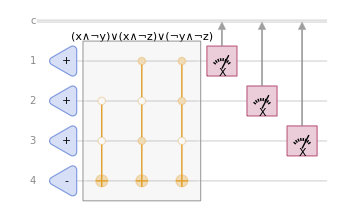

```mathematica
QuantumCircuitOperator["DeutschJozsa"[boo]]["Diagram"]
```

Pay close attention to the measurements. In Deutsch–Jozsa, the measurements are in the Pauli-X basis. The same circuit can also be presented in an equivalent form as follows.

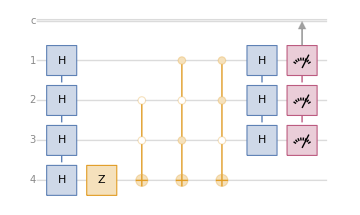

```mathematica
({"H"->Range[4],"Z"->4}/*QuantumCircuitOperator["DeutschJozsaBooleanOracle"[boo]]/*{"H"->Range[3],{1,2,3}})["Diagram"]
```

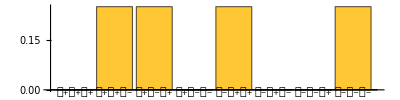

```mathematica
QuantumCircuitOperator["DeutschJozsa"[boo]][]["ProbabilitiesPlot",AspectRatio->1/4]
```

As one can see, the probability of getting +++ (equivalently, in the computational basis, it’d be 000) is zero. This implies that the function is a balanced one.

For the Deutsch–Jozsa phase oracle, as noted, there is no ancillary qubit. The overall circuit is:

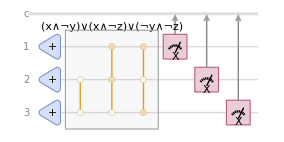

```mathematica
QuantumCircuitOperator["DeutschJozsaPhase"[boo]]["Diagram"]
```

As in the Boolean case, with the Deutsch–Jozsa phase oracle the probability of measuring +++  is also zero.

```mathematica
QuantumCircuitOperator["DeutschJozsaPhase"[boo]][]["ProbabilitiesPlot",AspectRatio->1/4]
```

-Graphics-

Consider the Deutsch–Jozsa outcome probabilities for 10 balanced Boolean functions on three input bits. In every case, the probability of measuring +++ is zero

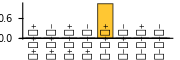
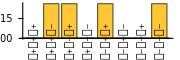
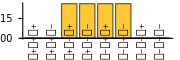
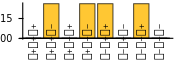
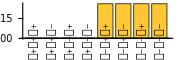
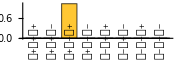
Boolean function Deutsch-Jozsa probabilities | 
!x | -Graphics-
(!x&&!y)||(!x&&!z)||(!y&&!z) | -Graphics-
(!x&&!y)||(!x&&z)||(!y&&!z) | -Graphics-
(!x&&y)||(!y&&!z) | -Graphics-
(x&&!y&&!z)||(!x&&y)||(!x&&z) | -Graphics-
(!x&&!y)||(!x&&!z)||(!y&&z) | -Graphics-
(!x&&!y)||(!x&&z)||(!y&&z) | -Graphics-
(x&&!y&&z)||(!x&&y)||(!x&&!z) | -Graphics-
(!x&&y)||(!y&&z) | -Graphics-
!y | -Graphics-

```mathematica
Grid[Prepend[Table[{BooleanConvert[bf][x,y,z],QuantumCircuitOperator["DeutschJozsa"[bf]][]["ProbabilitiesPlot",AspectRatio->1/3,ImageSize->Small,"LabelsAngle"->90Degree]},{bf,threeVariableBooleans["Balanced"][[;;10]]}],Style[#,Bold]&/@{"Boolean function""Deutsch-Jozsa probabilities"}],Frame->All,Alignment->{{Left,Center}}]
```

Consider the Deutsch–Jozsa outcome probabilities for the constant Boolean functions on three input bits. In every case, the probability of measuring +++ is one.

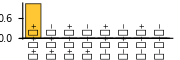
Boolean function Deutsch-Jozsa probabilities | 
False | -Graphics-
True | -Graphics-

```mathematica
Grid[Prepend[Table[{BooleanConvert[bf][x,y,z],QuantumCircuitOperator["DeutschJozsa"[bf]][]["ProbabilitiesPlot",AspectRatio->1/3,ImageSize->Small,"LabelsAngle"->90Degree]},{bf,threeVariableBooleans["Constant"]}],Style[#,Bold]&/@{"Boolean function""Deutsch-Jozsa probabilities"}],Frame->All,Alignment->{{Left,Center}}]
```

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

Define the deterministic classical Deutsch–Jozsa algorithm:

```mathematica
ClearAll[classicalDJ]
classicalDJ[boo_,allX_]:=Module[{decision=False},
Do[
If[Xor@@allX[[1]]!=Xor@@allX[[i]],
decision=True;
Return[Print["After "<>ToString[i]<>" queries, it is determined that the function is balanced"]],
Print["The result of query-"<>ToString[i]<>" is the same as previous one, so still cannot determined if the function is balanced or constant."]],{i,2,Length[allX]/2}];
With[{i=Length[allX]/2+1},
If[!decision,If[Xor@@allX[[1]]==Xor@@allX[[i]],Print["After "<>ToString[i]<>" queries, it is determined that the function is constant"],
Print["After "<>ToString[i]<>" queries, it is determined that the function is balanced"]]]]]
```